```mathematica
Exit[]
```

## init

```mathematica
Get["/data/mapk/mapkp4.mx"];
Get["/home/abergman/dicty/SPSA.m"]
```

```mathematica
LaunchKernels[]
ParallelEvaluate[$KernelID]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
lenX=Range[0.01,1.05,0.05]
lenX=Clip[lenX]
Length[lenX]

grad=Range[0,1.0,0.05]//Chop
Length[grad]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.01}

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.}

21

{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

21

```mathematica
{v,θ0}={{p4b, p2, p3a, p3b, p3c, p3d, p3e, p3f, p5, StotNative, StotOpt, StotOE, maxdose, dX}, {10, 1., 0.1, 0., 111., 6.0, 0.4, 1.1, 5., 1., 9., 90., 0.01, 0.0001}};
{v,θ0}={{p4b, p2, p3a, p3b, p3c, p3d, p3e, p3f, p5, StotNative, StotOpt, StotOE, maxdose, dX}, {8., 1., 0.1, 0.002, 106., 1.5, 1.5, 1.2, 5., 1.2, 3., 80., 0.01, 0.0001}};
inputθ0[]:=TableForm[Table[With[{i=i},{InputField[Dynamic[θ0[[i]]],Number,FieldSize->{11,1}],
Button["-",θ0[[i]]=0.9*θ0[[i]]],Button["+",θ0[[i]]=1.1*θ0[[i]]],
Button["-",θ0[[i]]=0.99*θ0[[i]]],Button["+",θ0[[i]]=1.01*θ0[[i]]]
}],{i,1,Length[θ0]}],TableHeadings->{v,{"θ0","-10%","+10%","-1%","+1%"}}]
```

```mathematica
tend=10000;
pθ0:=Thread[Rule[v,θ0]]
```

```mathematica
p3sigmoid=Function[s,p3[s]->((p3b-p3d)/(1+Exp[(Smem[s][t]-p3a)p3c])+p3d)(1/(1+Exp[(Smem[s][t]-p3e)p3f]))]/@{0,1};
```

```mathematica
myrunsim[{pp___},OptionsPattern[{lengthX:>lenX,slevel:>({StotNative,StotOE}/.pθ0),gradient:>grad}]]:=With[{p=Flatten[{pp}]},
DistributeDefinitions[θ0];
Transpose@ParallelTable[
plist=Join[p,
{λ->l,Stot->s,γ->g,δ[x_]->g*maxdose(l+dX*x),p1[x_]->p5*δ[x],p3sigmoid,p4[_]->p4b,MI->If[g*dX*maxdose==0,0,(MAPKpp[1]-MAPKpp[0])/(g*dX*maxdose)]}/.p/.pθ0,pθ0];
runsim[plist]
,{l,OptionValue[lengthX]},{s,OptionValue[slevel]},{g,OptionValue[gradient]},Method->"FinestGrained"]
]
```

```mathematica
DistributeDefinitions["Global`*"]
$DistributedContexts=None;
```

{Global`}

## Plots

### Scaffold dose response

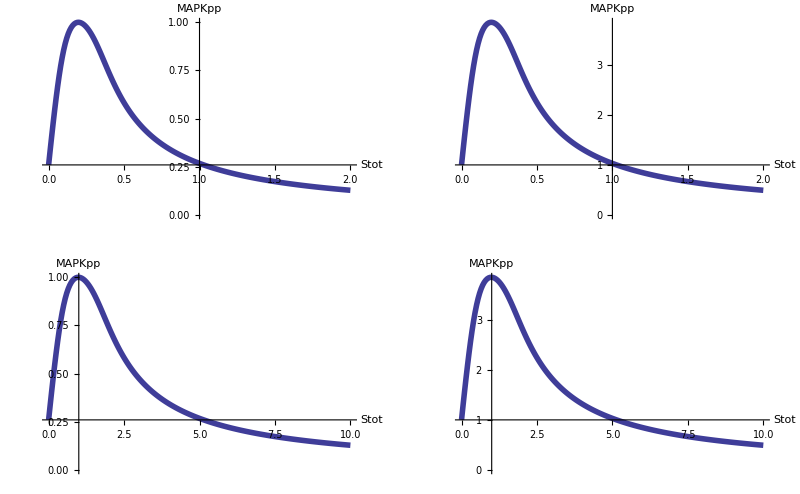

```mathematica
scaffoldDoseResponse=ParallelTable[{s,MAPKpp[0]}/.runsim[p4[_]->0,p2->0,Stot->s,p1[_]->100],{s,0.0,2.0,0.01}];
Table[
ListLinePlot[scaffoldDoseResponse/.{s_,m_}->{s/ss,m/ff},AxesOrigin->{1,scaffoldDoseResponse[[1,-1]]/ff},AxesLabel->{"Stot","MAPKpp"},PlotStyle->Thickness[0.01],BaseStyle->{FontSize->14}],{ss,{1,0.2}},{ff,{MAXMAPKPP,scaffoldDoseResponse[[1,-1]]}}]//GraphicsGrid[#,ImageSize->Full]&
```

### figs func

```mathematica
Off[Power::infy]
Off[Infinity::indet]
figs=Function[dat,GraphicsGrid[{{
ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"],
Plot[p3[0]/.dat[[1,1]]/.Smem[0][t]->Smem,{Smem,0,Max[Smem[0]/.dat]},PlotRange->All,AxesLabel->{"Smem","p3[Smem]"}]
},
{
ListLinePlot[{λ,Scyto[0]}/.dat,PlotLabel->"Scyto"],
ListLinePlot[{λ,Smem[0]}/.dat,PlotLabel->"Smem",PlotRange->All],
ListLinePlot[{λ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"]
},{
ListPlot[{(Stot-Smem[0]-Scyto[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",Joined->True,PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->{0,1},AxesLabel->{"Sves","MAPKpp"}]
,
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->{0,1}],
ListLinePlot[{λ,MI}//.dat/.ComplexInfinity->0,PlotRange->{-2,2},PlotLabel->"MI"]
}},ImageSize->Full]];
```

### Uniform stim, vesicle transport inhibition

```mathematica
Dynamic[
dat={myrunsim[dX->0,p3b->p3d],myrunsim[dX->0]};
GraphicsColumn[figs/@dat,ImageSize->Full]
,TrackedSymbols:>{θ0}
]
```

### Gradient stim

{2,21,1,75}

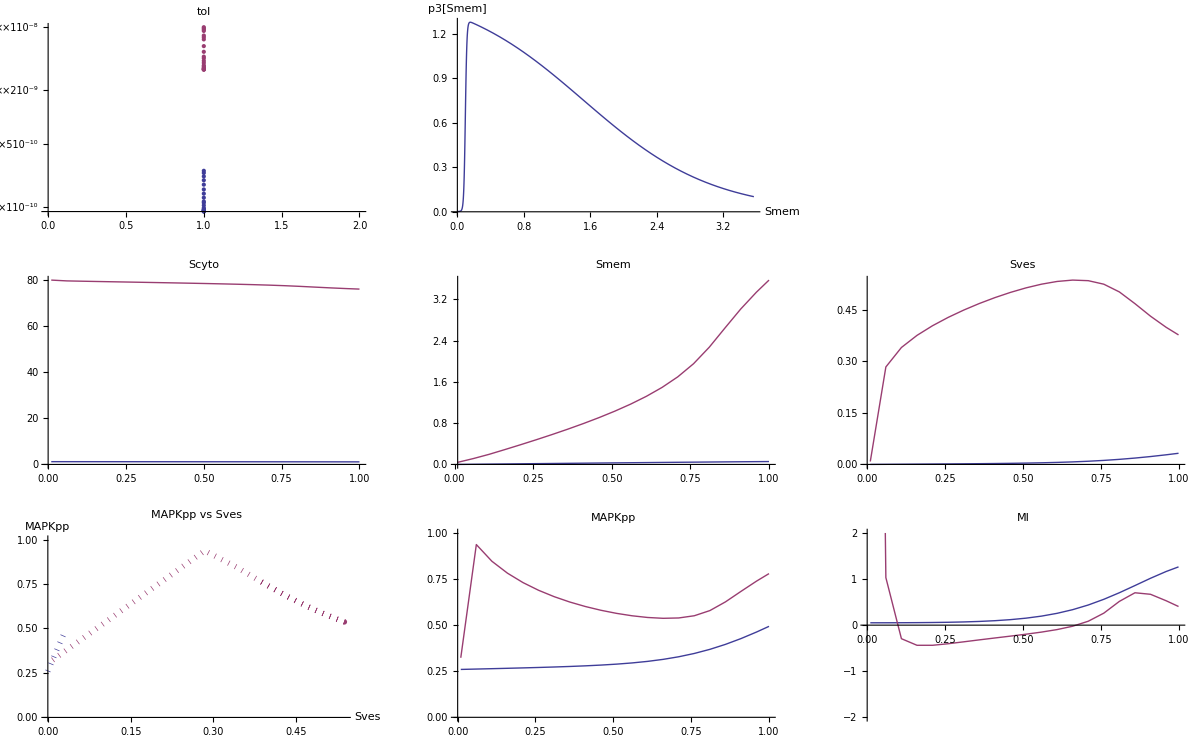

```mathematica
dat=myrunsim[{},gradient->{1}];
Dimensions[dat]
dat=Transpose[dat,{2,3,1,4}];
dat=Flatten[dat,1];
figs[dat]
```

### MI-MAPK vs Stot

```mathematica
dat=myrunsim[{},lengthX->Select[lenX,#>0.2&],gradient->{1},slevel->(Range[StotNative,StotOE,(StotOE-StotNative)/250.]/.pθ0)];
Dimensions[dat]
```

{251,17,1,75}

```mathematica
Block[{MI,ERK},
ERK={Stot/StotNative,(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)}/.dat//Transpose[#,{3,2,1}]&//Flatten[#,1]&//Mean;
MI={Stot/StotNative,MI}//.dat//Transpose[#,{3,2,1}]&//Flatten[#,1]&//Mean;
GraphicsGrid[{{
ListLinePlot[{λ,(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)}/.dat//Transpose[#,{2,3,1}]&//Flatten[#,1]&,PlotStyle->({Thickness[0.01],Hue[0.7,#,1]}&/@(Range[Length[dat]]/Length[dat])),AxesLabel->{"dose","MAPKpp"}],
ListLinePlot[{λ,MI}//.dat//Transpose[#,{2,3,1}]&//Flatten[#,1]&,PlotStyle->({Thickness[0.01],Hue[1,#,1]}&/@(Range[Length[dat]]/Length[dat])),AxesLabel->{"Dose","MI"},PlotRange->All]},
{
ListPlot[{ERKᵀ/{1,Max[ERK[[All,2]]]}//Transpose,MIᵀ/{1,Max[MI[[All,2]]]}//Transpose},Joined->True,PlotRange->{-0.5,1},Filling->Axis,AxesLabel->{"Scaffold","AU"},PlotStyle->Thick,PlotLegends->LineLegend[{"MAPKpp                         ","MI"}],ImageSize->Full
],SpanFromLeft
}},ImageSize->Full]]
```

-Graphics-

### MI vs grad

```mathematica
dat=myrunsim[{},lengthX->Select[lenX,#>0.2&],slevel->({StotNative,StotOpt}/.pθ0)];
Dimensions[dat]
```

{2,17,21,75}

```mathematica
GraphicsGrid[{
Function[{i,lbl},
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat[[i]]//Transpose,PlotLabel->lbl,PlotRange->{0,1},AxesLabel->{"dose","MAPKpp"},PlotStyle->({Thickness[0.01],Hue[0.7,#,1]}&/@grad)]]~MapThread~{{1,2},{"Native","Optimal"}},
Function[{i,lbl},
ListLinePlot[{λ,MI}//.dat[[i]]//Transpose,PlotRange->All,PlotLabel->lbl,AxesLabel->{"dose","MI"},
PlotStyle->({Thickness[0.01],Hue[1,#,1]}&/@grad)]
]~MapThread~{{1,2},{"Native","Optimal"}},{
ListLinePlot[{γ,MI}//.dat//Transpose//Mean,PlotMarkers->Automatic,PlotLegends->LineLegend[{"Native                       ","Optimal"}],AxesLabel->{"Gradient","MI"},PlotRange->All,ImageSize->Full],
SpanFromLeft}
},ImageSize->Full]
```

-Graphics-

### fig2/fig3

```mathematica
Dynamic[
GraphicsRow[{fig2[],fig3[]}],
TrackedSymbols:>{θ0},SynchronousUpdating->False
]
```

```mathematica
{{p3e,p3f,,,,,p4b,p2,p3a,p3b,p3c,p3d,p5,StotNative,StotOE,maxdose,dX},
{0.4,1.1,0.1,3.,0.13,6.,10,1.,0.1,0,111,6,5.,1.,80,0.01,0.0001}}ᵀ//Grid
```

p3e | 0.4
p3f | 1.1
 | 0.1
 | 3.
 | 0.13
 | 6.
p4b | 10
p2 | 1.
p3a | 0.1
p3b | 0
p3c | 111
p3d | 6
p5 | 5.
StotNative | 1.
StotOE | 80
maxdose | 0.01
dX | 0.0001

### pub figs

```mathematica
dat=myrunsim[{},gradient->{1}];
Dimensions[dat]
dat=Transpose[dat,{2,3,1,4}];
dat=Flatten[dat,1];
```

{2,21,1,75}

```mathematica
mybasestyle={FontWeight->"Bold", FontSize->14,Thickness[0.01]};
myaxisstyle={FontWeight->"Bold", FontSize->16,Thickness[0.01]};
mytitlestyle={FontWeight->"Bold", FontSize->18,Thickness[0.01]};
```

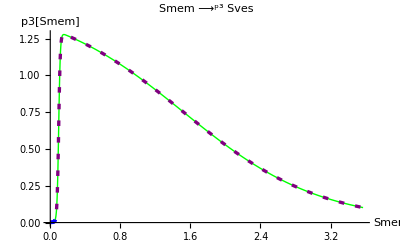

```mathematica
Show[
Plot[p3[0]/.dat[[1,1]]/.Smem[0][t]->Smem,{Smem,0,Max[Smem[0]/.dat]},PlotRange->All,AxesLabel->(Style[#,myaxisstyle]&/@{"Smem","p3[Smem]"}),PlotLabel->Style["Smem ⟶^p3 Sves",mytitlestyle],BaseStyle->mybasestyle,ImageSize->Full,PlotStyle->Green],
Plot[p3[0]/.dat[[1,1]]/.Smem[0][t]->Smem,{Smem,0,Max[Smem[0]/.dat[[2]]]},BaseStyle->mybasestyle,PlotStyle->{Purple,Dashing[{0.01,0.02}],Thickness[0.006]}],
Plot[p3[0]/.dat[[1,1]]/.Smem[0][t]->Smem,{Smem,0,Max[Smem[0]/.dat[[1]]]},BaseStyle->mybasestyle,PlotStyle->{Blue,Thickness[0.007]}]
]
```

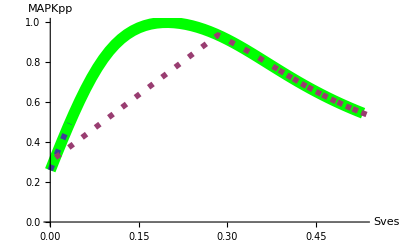

```mathematica
Show[
ListLinePlot[Select[scaffoldDoseResponse,#[[1]]<Max[(Stot-Smem[0]-Scyto[0])/.dat]&]/.{s_,m_}->{s,m/MAXMAPKPP},PlotStyle->{Green,Thickness[0.02]},PlotRange->{0,1},AxesLabel->(Style[#,myaxisstyle]&/@{"Sves","MAPKpp"}),BaseStyle->mybasestyle],
ListPlot[{(Stot-Smem[0]-Scyto[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->Style["MAPKpp vs Sves",mytitlestyle],Joined->True,PlotStyle->{{Dashing[{0.01,0.02}],Thickness[0.01]},Thickness[0.01]},BaseStyle->mybasestyle],ImageSize->Full]
```

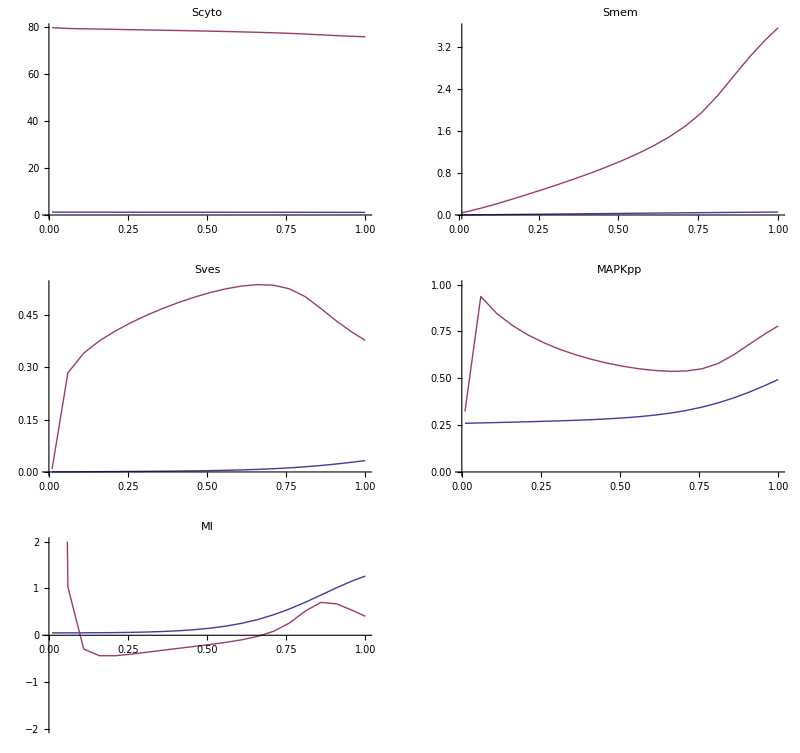

```mathematica
GraphicsGrid[{{
ListLinePlot[{λ,Scyto[0]}/.dat,PlotLabel->"Scyto",BaseStyle->mybasestyle],
ListLinePlot[{λ,Smem[0]}/.dat,PlotLabel->"Smem",PlotRange->All,BaseStyle->mybasestyle]
},{
ListLinePlot[{λ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves",BaseStyle->mybasestyle],
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->{0,1},BaseStyle->mybasestyle]
},{
ListLinePlot[{λ,MI}//.dat/.ComplexInfinity->0,PlotRange->{-2,2},PlotLabel->"MI",BaseStyle->mybasestyle]
}},ImageSize->Full]
```

```mathematica
dat=myrunsim[{},lengthX->Select[lenX,#>0.2&],gradient->{1},slevel->(Range[StotNative,StotOE,(StotOE-StotNative)/250.]/.pθ0)];
Dimensions[dat]
```

{251,17,1,75}

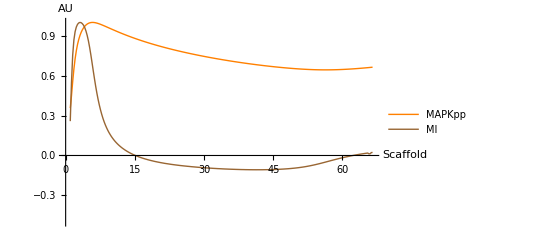

```mathematica
Block[{MI,ERK},
ERK={Stot/StotNative,(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)}/.dat//Transpose[#,{3,2,1}]&//Flatten[#,1]&//Mean;
MI={Stot/StotNative,MI}//.dat//Transpose[#,{3,2,1}]&//Flatten[#,1]&//Mean;

ListPlot[{ERKᵀ/{1,Max[ERK[[All,2]]]}//Transpose,MIᵀ/{1,Max[MI[[All,2]]]}//Transpose},Joined->True,PlotRange->{-0.5,1},AxesLabel->(Style[#,myaxisstyle]&/@{"Scaffold","AU"}),PlotStyle->{Orange,Brown},PlotLegends->LineLegend[{"MAPKpp","MI"}],ImageSize->Full,BaseStyle->mybasestyle]]
```

```mathematica
dat=myrunsim[{},lengthX->Select[lenX,#>0.2&],slevel->({StotNative,StotOpt}/.pθ0)];
Dimensions[dat]
```

{2,17,21,75}

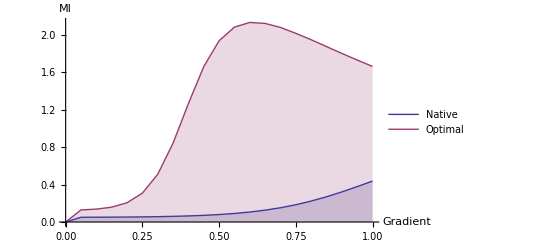

```mathematica
ListLinePlot[{γ,MI}//.dat//Transpose//Mean,PlotLegends->{"Native","Optimal"},AxesLabel->(Style[#,myaxisstyle]&/@{"Gradient","MI"}),PlotRange->All,ImageSize->Full,Filling->Axis,BaseStyle->mybasestyle]
```

## Opt

### Loss

```mathematica
Loss[θ_?(VectorQ[#,NumericQ]&)]:=Block[{pθ=Thread[v->Abs@θ]},
θ0=Abs[θ];
datGrad=myrunsim[{},gradient->{0.1,0.5,1},slevel:>{StotNative/.pθ0}];
datGrad=Flatten[datGrad,1];
datGrad=Mean[{γ,MI}//.datGrad];
equGrad=Fit[datGrad,{x},x];
errorGrad=Mean@Abs[datGrad[[All,2]]-(equGrad/.x->datGrad[[All,1]])];

dat=myrunsim[{},gradient->{1}];
dat=Transpose[dat,{2,3,1,4}];
dat=Flatten[dat,1];

SvesNative=(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])/.First[dat];

MAPKppNative=(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)/.First@dat;
MAPKppOE=(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)/.Last@dat;
{MIsimNative,MIsimOE}={λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat;

equNative=Fit[MIsimNative,{1,x},x];
MIerrorNative=Mean@Abs[MIsimNative[[All,2]]-(equNative/.x->lenX)];

equOE=Fit[Select[MIsimOE,1.8>#[[1]]>0.2&],{1,x},x];
MIerrorOE=Mean@Abs[MIsimOE[[All,2]]-(equOE/.x->lenX)];

lossfuncs=Hold[
StotNative^2/.pθ,
(StotOE/StotNative-9)^2/.pθ,
(Mean[MAPKppNative]-2.0*Mean[MAPKppOE])^2,
Mean[SvesNative]^2,
MIerrorNative,
MIerrorOE,
equNative/.a_+b_*x->(a-2)^2,
equNative/.a_+b_*x->b^2,
(equNative-2)^2/.Solve[equOE==equNative][[1]],
(x-0.8)^2/.Solve[equOE==equNative][[1]],
(x-0.2)^2/.Solve[equOE==0][[1]],
errorGrad,
(Last[datGrad][[2]]-2)^2
];
lossfuncsexp=List@@Map[Defer,lossfuncs];
lossfuncsval={ReleaseHold[lossfuncs]};

w.lossfuncsval
]
Loss[θ0]
```

31.4773

```mathematica
w=1/(Chop[lossfuncsval]/. 0->1.)
```

{1.,0.000152416,1.27968,154951.,13.0887,0.358743,0.221504,3.72208,0.336795,1581.38,5.93699,38.1508}

### FD

```mathematica
δp=0.010;
grad=FDGradientP[Loss,θ0,δp]
```

{0.81721,39.5965,568.804,-194.161,0.232853,-3.68512,-0.850399,-0.445491,-7.77229,-34.6731,0.,0.0217607,-2979.9,-744.979}

```mathematica
Loss[θ0]//ScientificForm
```

2.97664×10^1

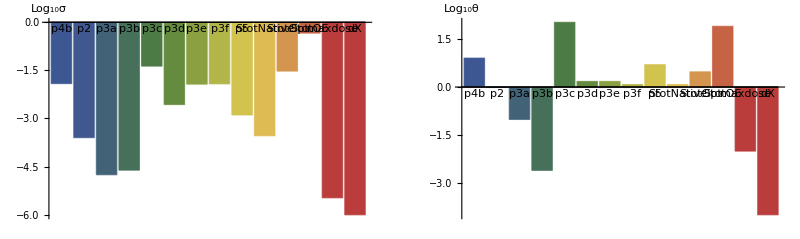

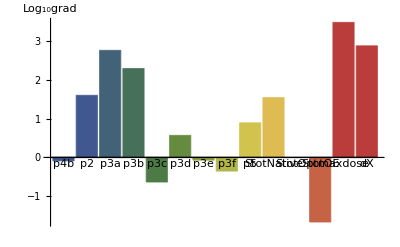

```mathematica
δL=10^-2;
σ0=δL/Abs@grad;
σ0=σ0/.ComplexInfinity->100;
σ0=MapThread[Function[{p,s},Clip[s,{0.,δp*p}]],{θ0,σ0}];
GraphicsRow[{
BarChart[Log[10,σ0],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"","Log_10σ"}],
BarChart[Log[10,θ0],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"","Log_10θ"}]},ImageSize->Full]
BarChart[Log[10,Abs@grad],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"","Log_10grad"},ImageSize->Full]
```

```mathematica
σ1=10^N@Floor@Log[10,σ0];
TableForm[{σ0,σ1}]
```

0.0122368 | 0.000252547 | 0.0000175807 | 0.000024446 | 0.0429456 | 0.00271361 | 0.0117592 | 0.0119968 | 0.00128662 | 0.000288408 | 0.03 | 0.459544 | 3.35582×10^-6 | 9.89995×10^-7
0.01 | 0.0001 | 0.00001 | 0.00001 | 0.01 | 0.001 | 0.01 | 0.01 | 0.001 | 0.0001 | 0.01 | 0.1 | 1.×10^-6 | 1.×10^-7

```mathematica
TableForm[{θ0,δp θ0,σ0,σ1,grad}//SetPrecision[#,2]&,TableHeadings->{{"θ0","δp.θ0","σ0","σ1","grad"},v}]
```

| p4b | p2 | p3a | p3b | p3c | p3d | p3e | p3f | p5 | StotNative | StotOpt | StotOE | maxdose | dX
θ0 | 8.1 | 0.97 | 0.096 | 0.0024 | 110. | 1.5 | 1.5 | 1.2 | 5. | 1.2 | 3. | 80. | 0.0098 | 0.000099
δp.θ0 | 0.081 | 0.0097 | 0.00096 | 0.000024 | 1.1 | 0.015 | 0.015 | 0.012 | 0.05 | 0.012 | 0.03 | 0.8 | 0.000098 | 9.9×10^-7
σ0 | 0.012 | 0.00025 | 0.000018 | 0.000024 | 0.043 | 0.0027 | 0.012 | 0.012 | 0.0013 | 0.00029 | 0.03 | 0.46 | 3.4×10^-6 | 9.9×10^-7
σ1 | 0.01 | 0.0001 | 0.00001 | 0.00001 | 0.01 | 0.001 | 0.01 | 0.01 | 0.001 | 0.0001 | 0.01 | 0.1 | 1.×10^-6 | 1.×10^-7
grad | 0.82 | 40. | 570. | -190. | 0.23 | -3.7 | -0.85 | -0.45 | -7.8 | -35. | 0 | 0.022 | -3000. | -740.

### Viz

```mathematica
viz:=Dynamic[
GraphicsGrid[{
{ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"],
Plot[p3[0]/.p3sigmoid/.Smem[0][t]->Smem//.dat[[1,1]],{Smem,0,Max[Smem[0]/.dat]},PlotRange->{p3d/.dat[[1,1]],0},AxesLabel->{"Smem","p3[Smem]"}],
Show[ListPlot[datGrad,AxesLabel->{"grad","MI"},PlotLabel->errorGrad,PlotRange->All,PlotStyle->PointSize[0.03]],Plot[equGrad,{x,0,1},PlotRange->All]]
},{
ListLinePlot[{λ,Scyto[0]}/.dat,PlotLabel->"Scyto"],
ListLinePlot[{λ,Smem[0]}/.dat,PlotLabel->"Smem"],
ListLinePlot[{λ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"]
},{
ListLinePlot[{(Stot-Smem[0]-Scyto[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->{0,1},AxesLabel->{"Sves","MAPKpp"}],
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->{0,1}],
Show[ListPlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->5*10^0{-1,1},AxesLabel->{"Dose","MI"},PlotLabel->(equNative/.a_+b_*x->a)],
Plot[{equNative,equOE},{x,0,1}]
]
}},ImageSize->Full]
,TrackedSymbols:>{dat}]
```

```mathematica
vizLossInput:=Table[With[{i=i},
{i,
InputField[Dynamic[w[[i]]],Number,FieldSize->{12,1}],
Dynamic[ScientificForm@SetPrecision[lossfuncsval[[i]],3]],
Dynamic[lossfuncsval[[i]]w[[i]]],
lossfuncsexp[[i]]
}],{i,1,Length[w]}]//TableForm[#,TableHeadings->{None,{"i","w","val","w.v","exp"}}]&
vizLossBar:=Dynamic[BarChart[w lossfuncsval//Reverse,BarOrigin->Left,ChartLabels->Reverse@lossfuncsexp,PlotRange->All,AspectRatio->0.3,ImageSize->Full]]
```

```mathematica
PlotRange->{{-0.51,2},All}
```

PlotRange→{{-0.51,2},All}

```mathematica
vizLossDiff[]:=Module[{},
{sol,Lhist}=SPSAGetHistory[];
θ0=Lhist[[-1,2]];
DistributeDefinitions[θ0];
Loss[θ0];
lossfuncsvalθ0=w lossfuncsval;
Dynamic[BarChart[w lossfuncsval-lossfuncsvalθ0//Reverse,BarOrigin->Left,ChartLabels->Reverse@lossfuncsexp,PlotRange->All,AspectRatio->0.3,ImageSize->Full]]
]
```

### Run

```mathematica
equNative/.Solve[equOE==equNative][[1]]
```

1.47385

```mathematica
w={0,0.00001,0,0,0.1,0.05,0,0,1.,1,0.1,40.,0.};
```

```mathematica
vizLossInput
```

i | w | val | w.v | exp
1 |  |  |  | StotNative^2/.pθ
2 |  |  |  | (StotOE/StotNative-9)^2/.pθ
3 |  |  |  | (Mean[MAPKppNative]-2. Mean[MAPKppOE])^2
4 |  |  |  | Mean[SvesNative]^2
5 |  |  |  | MIerrorNative
6 |  |  |  | MIerrorOE
7 |  |  |  | equNative/.a_+b_ x→(a-2)^2
8 |  |  |  | equNative/.a_+b_ x→b^2
9 |  |  |  | (equNative-2)^2/.Solve[equOE==equNative]⟦1⟧
10 |  |  |  | (x-0.8)^2/.Solve[equOE==equNative]⟦1⟧
11 |  |  |  | (x-0.2)^2/.Solve[equOE==0]⟦1⟧
12 |  |  |  | errorGrad
13 |  |  |  | (Last[datGrad]⟦2⟧-2)^2

```mathematica
σ1=SPSA`Private`σk
```

```mathematica
σ1=Table[1.,{Length[θ0]}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
SPSASetσ[σ1]
```

{0.01,0.0001,0.00001,0.00001,0.01,0.001,0.01,0.01,0.001,0.0001,0.01,0.1,1.×10^-6,1.×10^-7}

```mathematica
SPSAMaxEvals[1000]
RandomSearchInit[Loss,ToString/@v,θ0,σ1]
```

Start | Stop | Update | 
 | θk | σk | σmask
p4b |  |  | 
p2 |  |  | 
p3a |  |  | 
p3b |  |  | 
p3c |  |  | 
p3d |  |  | 
p3e |  |  | 
p3f |  |  | 
p5 |  |  | 
StotNative |  |  | 
StotOpt |  |  | 
StotOE |  |  | 
maxdose |  |  | 
dX |  |  |  |  |  |

```mathematica
Solve[equOE==equNative]
```

{{x→0.755914}}

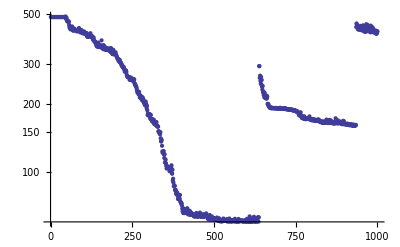

```mathematica
ListLogPlot[sol[[All,1]],PlotRange->All]
```

```mathematica
{sol,Lhist}=SPSAGetHistory[];
θ0=Lhist[[-1,2]]
DistributeDefinitions[θ0]
```

{0.0100908,1.0001,0.0660052,8.00079,1.25055,1.99623,0.998376,0.999789,0.0503687,0.998638,1.09799,908.45,0.0100075,0.000100442}

{}

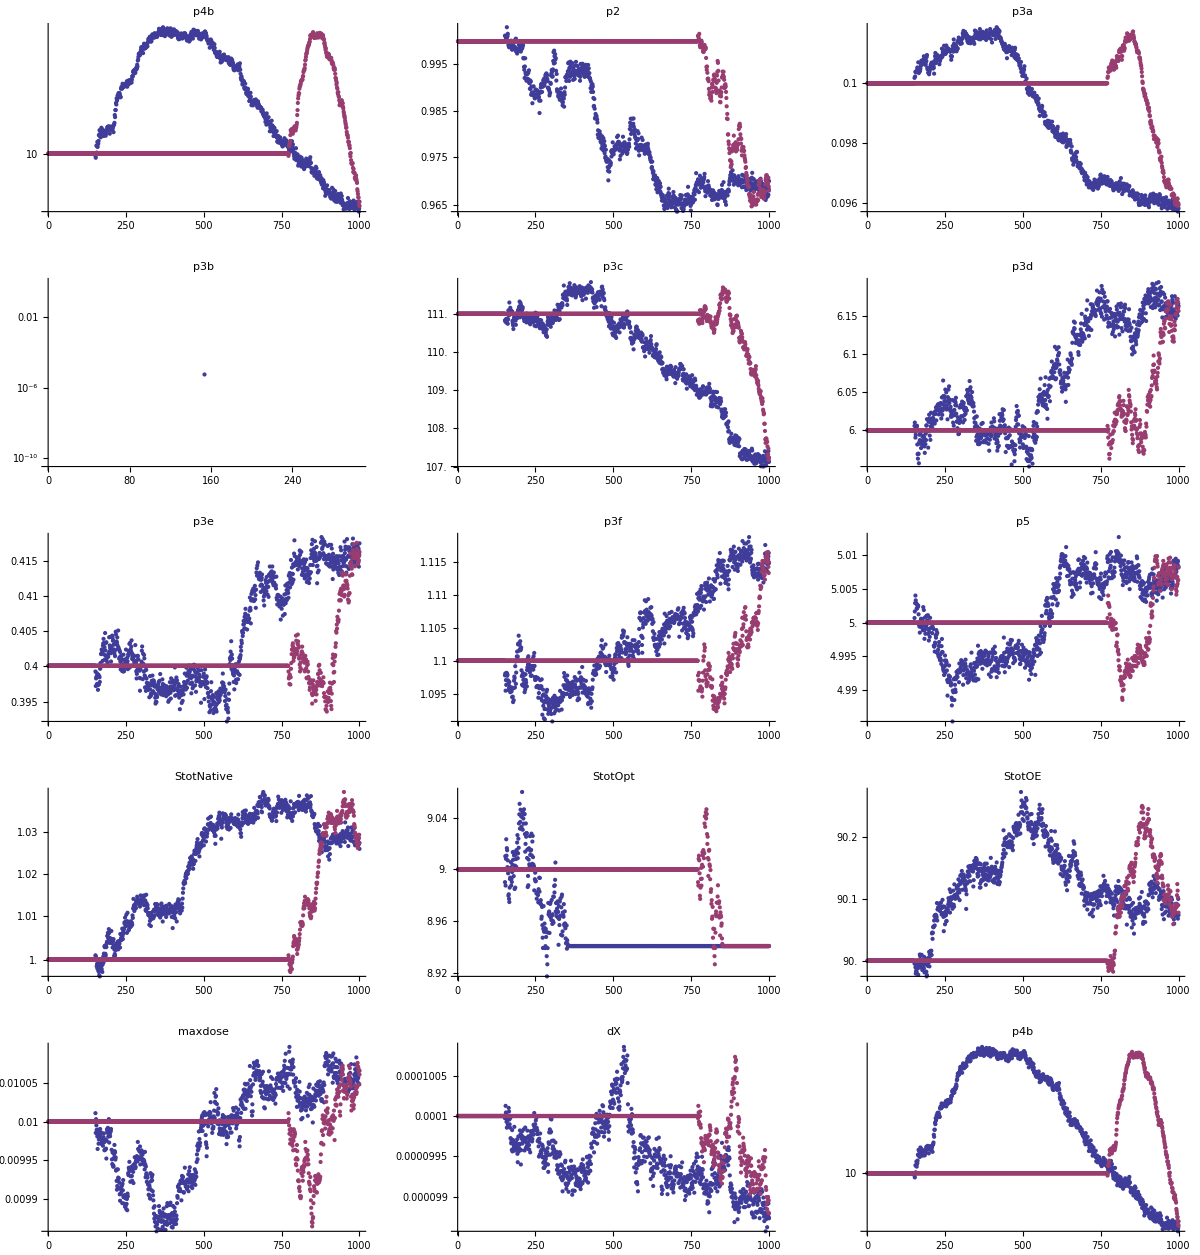

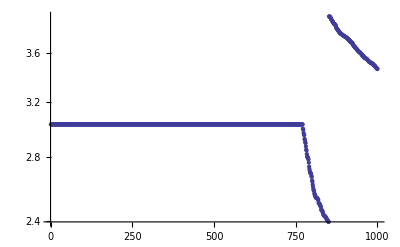

```mathematica
{sol,Lhist}=SPSAGetHistory[];
GraphicsGrid[MapThread[Function[{v,p,p2},ListLogPlot[{p,p2},PlotLabel->ToString[v],PlotRange->All]],{v,sol[[All,2]]ᵀ,Lhist[[All,2]]ᵀ}]//Partition[#,3,3,1]&,ImageSize->Full]
ListLogPlot[Lhist[[All,1]],PlotRange->All]
```

```mathematica
Dynamic[{MIerrorNative,MIerrorOE,equNative,StotNative,StotOE,Mean[SvesNative]}/.dat[[1,1]]]
```